```mathematica
ϵm[p_]:=√(me^2 c^4+(c p)^2)-me c^2;
ϵp[p_]:=√(me^2 c^4+(c p)^2)+me c^2;
ℏ=1.05457148×10^-34;
c=3×10^8;
me=9.10938188×10^-31;
AMU=1.66053886×10^-27;
ρ0=10^16;
((π^2 ℏ^3)/(me c)^3)^(1/3)
ρ0/AMU
((π^2 ℏ^3)/(me c)^3)ρ0/AMU
```

8.2775×10^-13

6.02214×10^42

3.41545×10^6

```mathematica
ne[η_,β_]:=NIntegrate[x^2/(Exp[β((1+x^2)^(1/2)-1)-η]+1),{x,0,∞}];
np[η_,β_]:=NIntegrate[x^2/(Exp[β((1+x^2)^(1/2)+1)+η]+1),{x,0,∞}];
Pe[η_,β_]:=NIntegrate[(x^4/√(1+x^2))/(Exp[β((1+x^2)^(1/2)-1)-η]+1),{x,0,∞}];
Pp[η_,β_]:=NIntegrate[(x^4/√(1+x^2))/(Exp[β((1+x^2)^(1/2)+1)+η]+1),{x,0,∞}];
ue[η_,β_]:=NIntegrate[(x^2(√(1+x^2)-1))/(Exp[β((1+x^2)^(1/2)-1)-η]+1),{x,0,∞}];
up[η_,β_]:=NIntegrate[(x^2(√(1+x^2)+1))/(Exp[β((1+x^2)^(1/2)+1)+η]+1),{x,0,∞}];
```

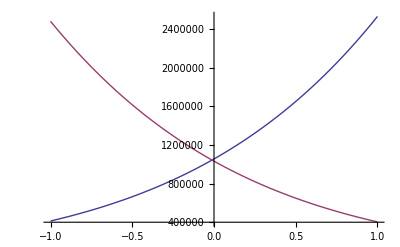

```mathematica
Plot[{ne[η,0.012],np[η,0.012]},{η,-1,1}]
```

```mathematica
η0[β_,Ye_]:=η/.Quiet[FindRoot[ne[η,β]-np[η,β]==Ye((π^2 ℏ^3)/(me c)^3)ρ0/AMU,{η,0.0}]]
η0dimless[β_,C_]:=η/.Quiet[FindRoot[ne[η,β]-np[η,β]==C,{η,0.0}]]
```

```mathematica
η0dimless[0.0012777,27364.195090]
η0dimless[0.0511100,27364.195090]
With[{β=0.0012777,cc=27364.195090},
ne[η0dimless[β,cc],β]-np[η0dimless[β,cc],β]-cc
]
```

-0.00126035

0.95623

-1.82954×10^-7

```mathematica
ScientificForm@{η0dimless[1.0,1.0],η0dimless[10.0,1.0],η0dimless[100.0,1.0]}
```

{-6.52504×10^-1,7.31606,7.54784×10^1}

```mathematica
0.08((π^2 ℏ^3)/(me c)^3)ρ0/AMU
```

273236.

```mathematica
ScientificForm@{
ne[1.0,1.0],
np[1.0,1.0],
ne[1.0,0.1],
np[1.0,0.1]}
ScientificForm@{
Pe[1.0,1.0],
Pp[1.0,1.0],
Pe[1.0,0.1],
Pp[1.0,0.1]}
ScientificForm@{
ue[1.0,1.0],
up[1.0,1.0],
ue[1.0,0.1],
up[1.0,0.1]}
```

{8.51861,2.17624×10^-1,4.69604×10^3,6.39016×10^2}

{2.97053×10^1,6.56258×10^-1,1.57144×10^5,1.95356×10^4}

{2.39093×10^1,9.54092×10^-1,1.5264×10^5,2.0205×10^4}

```mathematica
D[x^2/(Exp[β((1+x^2)^(1/2)-1)-η]+1),η]//FullSimplify
```

x^2/(2+2 Cosh[β-√(1+x^2) β+η])